# Constant Model

Supplementary File for “Feedback between coevolution and epidemiology can help or hinder the maintenance of genetic variation in host-parasite models” 
Authors: MacPherson, Keeling, and Otto
Last Updated: November 15th, 2020

```mathematica
Clear["Global`*"]
```

By running the following line, prior to compiling the notebook, will produce the plots found in the main text.

```mathematica
(*CreateDirectory[NotebookDirectory[]<>"Plots"]*)
```

## Deterministic Dynamics

Differential Equations

```mathematica
(*Symmetric Matching-alleles assumption*)
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
(*Conversion of counts to allele frequencies*)
pSub={nH[1,t]->κ fH pH[t],nH[2,t]->κ fH (1-pH[t]),nP[1,t]->κ fP pP[t],nP[2,t]->κ fP (1-pP[t])};
(*Denom=(Sum[β[i,j]α nH[i,t]nP[j,t],{j,1,2},{i,1,2}]+Sum[δ nH[i,t],{i,1,2}])/(κ fH);*)
```

dp_H/dt=gH[t]

```mathematica
gH[t_]:=(*1/Denom*)1/(fH κ)(Sum[β[i,j]α nH[i,t]nP[j,t] ((-Mod[i,2])+nH[1,t]/(fH κ)),{j,1,2},{i,1,2}]+Sum[δ nH[i,t]((-Mod[i,2])+nH[1,t]/(fH κ)),{i,1,2}])/.βSub/.pSub//FullSimplify
```

```mathematica
gH[t]//FullSimplify
```

fP (X-Y) α (-1+pH[t]) pH[t] (-1+2 pP[t])

dp_P/dt=gP[t]

```mathematica
gP[t_]:=(*1/Denom*)1/(fP κ)(Sum[β[i,j]α nH[i,t]nP[j,t]((Mod[j,2] M)-M nP[1,t]/(fP κ)),{j,1,2},{i,1,2}]+Sum[γ nP[j,t] (Mod[j,2]M-M nP[1,t]/(fP κ)),{j,1,2}])/.M->1/.βSub/.pSub//FullSimplify
```

```mathematica
gP[t]
```

-fH (X-Y) α (-1+2 pH[t]) (-1+pP[t]) pP[t]

Equilibria and Stability

```mathematica
equi=Solve[{gH[t]==0,gP[t]==0},{pH[t],pP[t]}]//FullSimplify
```

{{pH[t]→0,pP[t]→0},{pH[t]→1,pP[t]→0},{pH[t]→1/2,pP[t]→1/2},{pH[t]→0,pP[t]→1},{pH[t]→1,pP[t]→1}}

Stability of polymorphic equilibrium

```mathematica
jMtrx={{D[gH[t],pH[t]],D[gH[t],pP[t]]},{D[gP[t],pH[t]],D[gP[t],pP[t]]}}/.equi[[1]]
```

{{fP (X-Y) α,0},{0,-fH (X-Y) α}}

```mathematica
Eigenvalues[jMtrx]//FullSimplify
```

{fH (-X+Y) α,fP (X-Y) α}

These eigenvalues are purely imaginary.

Numerical Integration

```mathematica
Clear[nsolMoran]
nsolMoran[pars_,inits_]:=nsolMoran[pars,inits]=NDSolve[{D[pH[t],t]==gH[t]/.pars,D[pP[t],t]==gP[t]/.pars,pH[0]==pH0/.inits,pP[0]==pP0/.inits},{pH[t],pP[t]},{t,0,tMax/.pars}]//Flatten
(*Allele frequency dynamics*)
pHsol[τ_,pars_,inits_]:=pH[t]/.nsolMoran[pars,inits]/.{t->τ}
pPsol[τ_,pars_,inits_]:=pP[t]/.nsolMoran[pars,inits]/.{t->τ}
```

Parameters used for Figure 1

```mathematica
TestPars={X->0.8,Y->0.4,κ->100,δ->1,α->0.2,γ->1,fH->1.3,fP->0.8,tMax->1000};
TestInits0={pH0->0.55,pP0->0.45};
TestInits={pH0->0.85,pP0->0.15};
TestInits2={pH0->0.7,pP0->0.3};
```

Plot allele frequency dynamics of deterministic model.

```mathematica
DetDynAF[pars_,inits_,color_,tMax_]:=Show[ListLinePlot[Table[{pHsol[τ,pars,inits],pPsol[τ,pars,inits]},{τ,0,tMax}],PlotRange->{{0,1},{0,1}},PlotStyle->color]/.Line[x_]:>{Arrowheads[Table[.05,{r,{2}}]],Arrow[x]},ListPlot[{{pH0,pP0}/.inits},PlotStyle->Red,PlotMarkers->{●,14}],AspectRatio->1,ImageSize->Medium,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]
```

Plot the dynamics of expected heterozygosity in the host.

```mathematica
DetDynHet[pars_,inits_,color_]:=Show[ListLinePlot[Table[2pHsol[τ,pars,inits](1-pHsol[τ,pars,inits]),{τ,0,1000}],PlotRange->{0,0.5},PlotStyle->color],ListPlot[{{0,2pH0(1-pH0)}/.inits},PlotStyle->Red,PlotMarkers->{●,14}],ImageSize->Medium,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]
```

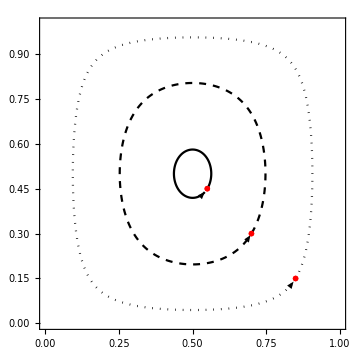

```mathematica
Show[DetDynAF[TestPars,TestInits0,Black,150],DetDynAF[TestPars,TestInits2,Directive[Black,Dashed],168],DetDynAF[TestPars,TestInits,Directive[Black,Dotted],212],Background->White]
Export[NotebookDirectory[]<>"Plots/Const_Det_AF.pdf",%,ImageResolution->300];
```

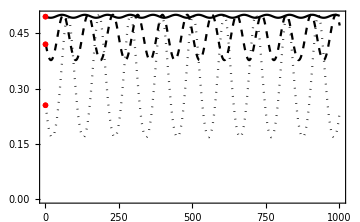

```mathematica
Show[DetDynHet[TestPars,TestInits0,Black],DetDynHet[TestPars,TestInits2,Directive[Black,Dashed]],DetDynHet[TestPars,TestInits,Directive[Black,Dotted]],Background->White]
Export[NotebookDirectory[]<>"Plots/Const_Det_Het.pdf",%,ImageResolution->300];
```

Neutral Expectation

Heterozygosity after k events 1/2(1-2/κ^2)^k given the initial heterozygosity of H_0=1/2.  Probability of k events by time ((κ t)^k Exp[-κ t])/(k!)

```mathematica
Clear[neutExp]
neutExp[κ_,t_]:=Sum[((fH κ t)^k Exp[-fH κ t])/(k!)1/2(1-2/(fH κ)^2)^k,{k,0,∞}]
```

This simplifies to:

```mathematica
Sum[((fH κ t)^k Exp[-fH κ t])/(k!)1/2(1-2/(fH κ)^2)^k,{k,0,∞}]
```

1/2 ⅇ^(-(2 t)/(fH κ))

## Ensemble Moments

Not used in the main text.  Is presented only for completeness.

Substitutions

### Moment Substitutions

```mathematica
first={δH->μδH,δP->μδP};
```

```mathematica
second=Block[{out},out={};
AppendTo[out,Solve[CδHH==Expand[(δH-μδH)^2]/.δH^2->X,X][[1]]/.first/.X->δH^2];
AppendTo[out,Solve[CδHP==Expand[(δH-μδH)(δP-μδP)]/.δH δP->X,X][[1]]/.first/.X->δH δP];
AppendTo[out,Solve[CδPP==Expand[(δP-μδP)^2]/.δP^2->X,X][[1]]/.first/.X->δP^2];
Flatten[out]
];
```

```mathematica
third=Block[{out},out={};
AppendTo[out,Solve[CδHHH==Expand[(δH-μδH)^3]/.δH^3->X,X][[1]]/.second/.first/.X->δH^3];
AppendTo[out,Solve[CδHHP==Expand[(δH-μδH)^2(δP-μδP)]/.δH^2 δP->X,X][[1]]/.second/.first/.X->δH^2 δP];
AppendTo[out,Solve[CδHPP==Expand[(δH-μδH)(δP-μδP)^2]/.δH δP^2->X,X][[1]]/.second/.first/.X->δH δP^2];
AppendTo[out,Solve[CδPP==Expand[(δP-μδP)^3]/.δP^3->X,X][[1]]/.second/.first/.X->δP^3];
Flatten[out]
];
```

```mathematica
fourth=Block[{out},out={};
AppendTo[out,Solve[CδHHHH==Expand[(δH-μδH)^4]/.δH^4->X,X][[1]]/.third/.second/.first/.X->δH^4];
AppendTo[out,Solve[CδHHHP==Expand[(δH-μδH)^3(δP-μδP)]/.δH^3 δP->X,X][[1]]/.third/.second/.first/.X->δH^3 δP];
AppendTo[out,Solve[CδHHPP==Expand[(δH-μδH)^2(δP-μδP)^2]/.δH^2 δP^2->X,X][[1]]/.third/.second/.first/.X->δH^2 δP^2];
AppendTo[out,Solve[CδHPPP==Expand[(δH-μδH)(δP-μδP)^3]/.δH δP^3->X,X][[1]]/.third/.second/.first/.X->δH δP^3];
AppendTo[out,Solve[CδPPPP==Expand[(δP-μδP)^4]/.δP^4->X,X][[1]]/.third/.second/.first/.X->δP^4];
Flatten[out]
];
```

### Simplification

```mathematica
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
```

```mathematica
nSub={nH[1]->H,nH[2]->fH κ-H,nP[1]->P,nP[2]->fP κ-P};
```

counts to deviations

Let δH=H-Ĥ and δP=P-P̂.  We will assume that the deviations from equilibrium, δH and δP, are small.

Note that the covariance between the deviations from equilibrium are equal to the the covariance in the original variables.

```mathematica
eSub={H->fH κ/2+ϵ δH,P->fP κ/2+ϵ δP};
```

```mathematica
μeSubRev={μδH->μH[τ]-fH κ/2,μδP->μP[τ]-fP κ/2,CδHH-> CHH[τ],CδHP->CHP[τ],CδPP->CPP[τ],CδHHH->CHHH[τ],CδHHP->CHHP[τ],CδHPP-> CHPP[τ],CδPPP->CPPP[τ]};
```

### Moment Closure

```mathematica
assump1={CδHH->0,CδHP->0,CδPP->0};
```

```mathematica
assump2={CδHHH->0,CδHHP->0,CδHPP->0,CδPPP->0};
```

```mathematica
assump3={CδHHHH->0,CδHHHP->0,CδHHPP->0,CδHPPP->0,CδPPPP->0};
```

Rates f[x] and change in x

```mathematica
d[H_,P_]:=(Sum[α β[h,p]nH[h]nP[p],{h,1,2},{p,1,2}]+Sum[δ nH[h],{h,1,2}])/(κ fH)/.nSub/.βSub//FullSimplify
```

```mathematica
f[H_,P_]:=Join[(*Host Free-living death*)Flatten[Table[(δ nH[h1])/d[H,P] nH[h2]/(fH κ)/.nSub,{h1,1,2},{h2,1,2}]],(*Infectious Death of h1 by p1, h2 born,p2 born*)Flatten[Table[(α β[h1,p1])/d[H,P] nH[h1]nP[p1] nH[h2]/(fH κ)nP[p2]/(fP κ)/.nSub/.βSub,{h1,1,2},{p1,1,2},{h2,1,2},{p2,1,2}]],(*Pathogen Free-living death*)Flatten[Table[(γ nP[p1])/d[H,P] nP[p2]/(fP κ)/.nSub,{p1,1,2},{p2,1,2}]]]//FullSimplify
```

```mathematica
ΔH=Join[(*Host Free-living death*)Flatten[Table[-Mod[h1,2]+Mod[h2,2],{h1,1,2},{h2,1,2}],1],(*Infectious Death of h1 by p1, h2 born,p2 dies*)Flatten[Table[-Mod[h1,2]+Mod[h2,2],{h1,1,2},{p1,1,2},{h2,1,2},{p2,1,2}]],(*Pathogen Free-living death*)Flatten[Table[0,{p1,1,2},{p2,1,2}]]]
```

{0,-1,1,0,0,0,-1,-1,0,0,-1,-1,1,1,0,0,1,1,0,0,0,0,0,0}

```mathematica
ΔP=Join[(*Natural death of h1 birth of h2*)Flatten[Table[0,{h1,1,2},{h2,1,2}],1],(*Infectious Death of h1 by p1, h2 born,p2 dies*)Flatten[Table[Mod[p1,2]-Mod[p2,2],{h1,1,2},{p1,1,2},{h2,1,2},{p2,1,2}]],(*Natural death of p1 birth of p2*)Flatten[Table[-Mod[p1,2]+Mod[p2,2],{p1,1,2},{p2,1,2}]]]
```

{0,0,0,0,0,1,0,1,-1,0,-1,0,0,1,0,1,-1,0,-1,0,0,-1,1,0}

Differential Equations

### Means

```mathematica
Clear[dμHdt]
dμHdt[t_]:=dμHdt[t]=Collect[Normal[Series[Simplify[f[H,P].ΔH]/.eSub,{ϵ,0,2}]],{ϵ,δH,δP},FullSimplify]/.third/.second/.first/.{ϵ->1}/.μeSubRev/.{τ->t}//Simplify
```

```mathematica
Clear[dμPdt]
dμPdt[t_]:=dμPdt[t]=Collect[Normal[Series[Simplify[f[H,P].ΔP]/.eSub,{ϵ,0,2}]],{ϵ,δH,δP},FullSimplify]/.third/.second/.first/.{ϵ->1}/.μeSubRev/.{τ->t}//Simplify
```

### Variances

```mathematica
Clear[dHHdt]
dHHdt[t_]:=dHHdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^2-H^2]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}(*FullSimplify[Collect[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^2-H^2]/.eSub],{ϵ,0,3}]],{ϵ,δH,δP},FullSimplify]/.third/.second/.first/.{ϵ->1}]/.μeSubRev/.{τ->t}//FullSimplify*)
```

```mathematica
Clear[dHPdt]
dHPdt[t_]:=dHPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)(P+ΔP)-H P]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dPPdt]
dPPdt[t_]:=dPPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(P+ΔP)^2-P^2]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dCHHdt,dCHPdt,dCPPdt]
dCHHdt[t_]:=(*dCHHdt[i,j,M,t]=*)dHHdt[t]-μH[t]dμHdt[t]-μH[t]dμHdt[t]
dCHPdt[t_]:=(*dCHPdt[i,j,M,t]=*)dHPdt[t]-μH[t]dμPdt[t]-μP[t]dμHdt[t]
dCPPdt[t_]:=(*dCPPdt[i,j,M,t]=*)dPPdt[t]-μP[t]dμPdt[t]-μP[t]dμPdt[t]
```

### Skews

```mathematica
Clear[dHHHdt]
dHHHdt[t_]:=dHHHdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^3-H^3]/.eSub],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dHHPdt]
dHHPdt[t_]:=dHHPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^2(P+ΔP)-H^2 P]/.eSub],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dHPPdt]
dHPPdt[t_]:=dHPPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)(P+ΔP)^2-H P^2]/.eSub],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dPPPdt]
dPPPdt[t_]:=dPPPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(P+ΔP)^3-P^3]/.eSub],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dCHHHdt]
dCHHHdt[t_]:=dCHHHdt[t]=dHHHdt[t]-μH[t]dCHHdt[t]-μH[t]dCHHdt[t]-μH[t]dCHHdt[t]-dμHdt[t]CHH[t]-dμHdt[t]CHH[t]-dμHdt[t]CHH[t]-μH[t]μH[t]dμHdt[t]-μH[t]μH[t]dμHdt[t]-μH[t]μH[t]dμHdt[t]
Clear[dCHHPdt]
dCHHPdt[t_]:=dCHHPdt[t]=dHHPdt[t]-μH[t]dCHPdt[t]-μH[t]dCHPdt[t]-μP[t]dCHHdt[t]-dμHdt[t]CHP[t]-dμHdt[t]CHP[t]-dμPdt[t]CHH[t]-μH[t]μH[t]dμPdt[t]-μH[t]μP[t]dμHdt[t]-μH[t]μP[t]dμHdt[t]
Clear[dCHPPdt]
dCHPPdt[t_]:=dCHPPdt[t]=dHPPdt[t]-μH[t]dCPPdt[t]-μP[t]dCHPdt[t]-μP[t]dCHPdt[t]-dμHdt[t]CPP[t]-dμPdt[t]CHP[t]-dμPdt[t]CHP[t]-μH[t]μP[t]dμPdt[t]-μH[t]μP[t]dμPdt[t]-μP[t]μP[t]dμHdt[t]
Clear[dCPPPdt]
dCPPPdt[t_]:=dCPPPdt[t]=dPPPdt[t]-μP[t]dCPPdt[t]-μP[t]dCPPdt[t]-μP[t]dCPPdt[t]-dμPdt[t]CPP[t]-dμPdt[t]CPP[t]-dμPdt[t]CPP[t]-μP[t]μP[t]dμPdt[t]-μP[t]μP[t]dμPdt[t]-μP[t]μP[t]dμPdt[t]
```

### Genetic Variance

```mathematica
D[2/(fH κ)μH[t]-2/(fH κ)^2(μH[t]^2+CHH[t]),t]
```

(2 μH'[t])/(fH κ)-(2 (CHH'[t]+2 μH[t] μH'[t]))/(fH^2 κ^2)

```mathematica
dHetdt[t_]:=(2 dμHdt[t])/(fH κ)-(2 (dCHHdt[t]+2 μH[t] dμHdt[t]))/(fH κ)^2
```

```mathematica
nearEquSub={μH[t]->fH κ/2+ϵ μdH[t],μP[t]->fP κ/2+ϵ μdH[t],CHH[t]->0+ϵ CδHH[t],CHP[t]->0+ϵ CδHP[t],CPP[t]->0+ϵ CδPP[t],CHHH[t]->0+ϵ CδHHH[t],CHHP[t]->0+ϵ CδHHP[t],CHPP[t]->0+ϵ CδHPP[t],CPPP[t]->0+ϵ CδPPP[t]};
```

If we are very near equilibrium then the ensemble moment dynamics of heterozygosity are equal to that of the neutral expectation

```mathematica
Normal[Series[dHetdt[t]/.nearEquSub/.{κ->1/ϵ},{ϵ,0,1}]]/.{ϵ->1/κ}//FullSimplify
```

-1/(fH κ)

```mathematica
neutExp[κ,t]
```

1/2 ⅇ^(-(2 t)/(fH κ))

```mathematica
Simplify[Normal[Series[D[neutExp[κ,t],t]/.{t->ϵ τ,κ->1/ϵ},{ϵ,0,1}]]/.{ϵ->1/κ},Assumptions->{τ>0}]
```

-1/(fH κ)

Numerical Integration

## Functions

```mathematica
Clear[odesEM]
```

```mathematica
TestPars={X->0.9,Y->0.7,α->0.2,γ->0.5,δ->0.5,fH->0.9,fP->0.6,κ->10000};
```

```mathematica
initsSubEM[pars_]:={μH[0]->fH κ/2,μP[0]->fP κ/2,CHH[0]->0,CHP[0]->0,CPP[0]->0,CHHH[0]->0,CHHP[0]->0,CHPP[0]->0,CPPP[0]->0}/.pars;
```

```mathematica
initsEM[pars_]:={μH[0]==fH κ/2,μP[0]==fP κ/2,CHH[0]==0,CHP[0]==0,CPP[0]==0,CHHH[0]==0,CHHP[0]==0,CHPP[0]==0,CPPP[0]==0}/.pars;
```

```mathematica
odesEM[pars_]:={D[μH[t],t]==dμHdt[t],D[μP[t],t]==dμPdt[t],D[CHH[t],t]==dCHHdt[t],D[CHP[t],t]==dCHPdt[t],D[CPP[t],t]==dCPPdt[t],D[CHHH[t],t]==dCHHHdt[t],D[CHHP[t],t]==dCHHPdt[t],D[CHPP[t],t]==dCHPPdt[t],D[CPPP[t],t]==dCPPPdt[t]}/.pars;
```

```mathematica
varsEM={μH[t],μP[t],CHH[t],CHP[t],CPP[t],CHHH[t],CHHP[t],CHPP[t],CPPP[t]};
```

```mathematica
Clear[nsolEM]
nsolEM[pars_,tMax_]:=nsolEM[pars,tMax]=NDSolve[Join[odesEM[pars],initsEM[pars]],varsEM,{t,0,tMax}][[1]]
```

```mathematica
nHet[pars_,tMax_,τ_]:=2/(fH κ)μH[t]-2/(fH κ)^2(μH[t]^2+CHH[t])/.nsolEM[pars,tMax]/.pars/.{t->τ}
```

## Plotting

```mathematica
Dequ=(Sum[β[h,p]α (fH κ)/2(fP κ)/2,{h,1,2},{p,1,2}]+δ fH κ)/(fH κ)/.βSub//Simplify;
```

```mathematica
Parsγ[γin_,δin_]:={fH->0.9,fP->0.6,X->0.9,Y->0.7,α->0.2,γ->γin,δ->δin,κ->100000};
ΔHEM[pars_,τ_]:=nHet[pars,τ,τ]-neutExp[κ,τ]/.pars
```

```mathematica
γDeivEM=Block[{Xr,Yr,αr,γr,δr,out,ct,pars},out={};
For[ct=1,ct≤200,ct++,
γr=RandomReal[{0.1,1}];δr=RandomReal[{0.1,1}];
AppendTo[out,{γr,δr,Dequ/.Parsγ[γr,δr],ΔHEM[Parsγ[γr,δr],50/fH/.Parsγ[γr,δr]]}]
];
out
];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

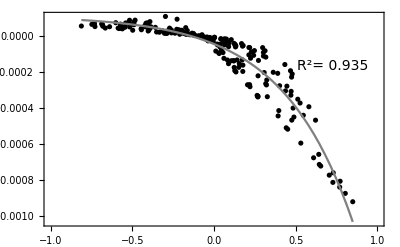

```mathematica
γDeivEMPlot=Module[{data},data=Transpose[{γDeivEM[[;;,1]]-γDeivEM[[;;,2]],γDeivEM[[;;,4]]}];
(*lmEM=LinearModelFit[data,x,x];*)
lmEM=NonlinearModelFit[data,y0+L/(1+Exp[-k(x-x0)]),{y0,L,k,x0},x];
Show[ListPlot[data,Frame->True,PlotStyle->Black],Plot[lmEM[x],{x,Min[data[[;;,1]]],Max[data[[;;,1]]]},PlotStyle->Gray],PlotRange->{{-1,1},Automatic},Epilog->Text[Style["R^2= "<>ToString[Round[lmEM["RSquared"],0.001]],14,Black],Scaled[{0.85,0.75}]],ImageSize->{Automatic,300},FrameTicksStyle->Directive[Black,Bold,14]]
]
Export[NotebookDirectory[]<>"Plots/gammaDeivEM.pdf",γDeivEMPlot,ImageResolution->500];
```

## Individual-based simulations

Picking Parameters

### Randomly choosing parameters

Randomly draws npts parameter combinations across parameter space.

```mathematica
Clear[randParsConst]
randParsConst[npts_]:=randParsConst[npts]=Block[{out,ct,a,x,y,d,g,fHr, fPr},out={};
For[ct=1,ct≤npts,ct++,
fHr=1;
fPr=1;
x=RandomReal[];y=RandomReal[{0,x}];
d=RandomReal[{0.1,1}];
g=RandomReal[{0.1,1}];a=RandomReal[{0,1}];
AppendTo[out,{fH->fHr,fP->fPr,X->x,Y->y,α->a,δ->d,γ->g}];
];
out
]
```

```mathematica
pars1=randParsConst[100];
```

### Fitting the epidemiological model

Gives parameter combination to be used in the constant size model given parameters in the epidemiological model for model comparison.

```mathematica
Clear[randPars2Const]
randPars2Const[epiPars_]:=randPars2Const[epiPars]=Block[{out,ct,a,x,y,d,g,fHr, fPr},out={};
For[ct=1,ct≤Length[epiPars],ct++,
fHr=(b X+b Y-X α-Y α-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))))/(2 b (X+Y))/.epiPars[[ct]];
fPr=-1/(2 b (X+Y))(-b X-b Y+4 b α+X α+Y α+4 b γ+4 b δ+X δ+Y δ-√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))))/.epiPars[[ct]];
x=(X/.epiPars[[ct]]);y=(Y/.epiPars[[ct]]);
d=(δ/.epiPars[[ct]]);
g=(δ/.epiPars[[ct]])fHr/fPr;
a=(α/(α+δ)/.epiPars[[ct]]);
AppendTo[out,{fH->fHr,fP->fPr,X->x,Y->y,α->a,δ->d,γ->g}];
];
out
]
```

## Making Input File

```mathematica
epiPars=randPars2Epi[100];
```

```mathematica
κSol[K_,pars_]:=κ/.Flatten[Solve[(fH κ/.pars)==K,κ]]
```

```mathematica
nRep=7;
nDemes=1000;
gmax=500;
```

```mathematica
constFile[pars_]:=Block[{out,rep},
out="Input file for Ecological simulations

number of reps (nRep): "<> ToString[nRep]<>"
number of demes (nDemes): "<> ToString[nDemes]<>"
maximum number of generations (gmax): "<> ToString[gmax]<>"
relative host size (fH): "<> ToString[fH/.pars]<>"
relative path size (fP): "<> ToString[fP/.pars]<>"
matching infection rate (X): "<> ToString[X/.pars]<>"
mismatching infection rate (Y): "<> ToString[Y/.pars]<>"
host natural death rate (delta): "<> ToString[δ/.pars]<>"
death probability (alpha): "<> ToString[α/.pars]<>"
pathogen death rate (gamma): "<>ToString[γ/.pars]<>"
carrying capacity (kappa): ";
For[rep=0,rep<nRep,rep++,out=out<>ToString[κSol[10^(2+0.25*rep),pars]]<>" "];
out
]
```

```mathematica
Do[Export[NotebookDirectory[]<>"/sims_11_1/inputConst_"<>ToString[i]<>".txt",constFile[randPars2Const[epiPars][[i]]]],{i,1,Length[epiPars]}]
```

Importing Data

## Parameters

Importing parameters used in the individual model analysis.  Fixed values of fH=fP.

```mathematica
(*Random Parameters fH=fP*)
fileC=NotebookDirectory[]<>"sims_11_1/const_11_20/runConst_";
fileC2=NotebookDirectory[]<>"sims_11_1/const_11_20/";
nRuns=100;
```

Importing parameters used in the cross-model comparison.

```mathematica
(*(*Model Comparison*)
fileC=NotebookDirectory[]<>"sims_11_1/const_11_20_2/runConst_";
fileC2=NotebookDirectory[]<>"sims_11_1/const_11_20_2/";
nRuns=100;*)
```

### Input New

```mathematica
Clear[pars]
pars[file_,run_]:=pars[file,run]=Import[file<>ToString[run]<>"/out.csv"]
```

```mathematica
Clear[nDemes,nRep,fH,fP,δ,X,Y,α,γ,κ]
nRep[file_,run_]:=pars[file,run][[2,2]]
nDemes[file_,run_]:=pars[file,run][[3,2]]
gmax[file_,run_]:=pars[file,run][[4,2]]
fH[file_,run_]:=pars[file,run][[5,2]]
fP[file_,run_]:=pars[file,run][[6,2]]
X[file_,run_]:=pars[file,run][[7,2]]
Y[file_,run_]:=pars[file,run][[8,2]]
δ[file_,run_]:=pars[file,run][[9,2]]
α[file_,run_]:=pars[file,run][[10,2]]
γ[file_,run_]:=pars[file,run][[11,2]]
κ[file_,run_,rep_]:=pars[file,run][[12,1+rep]];
```

Simulation parameters.  File, assigned above, determines whether which set of simulations to consider.  Run (between 1 and 100) determines the parameters, and rep (between 1 and 7) determines the population size.

```mathematica
simPars[file_,run_,rep_]:={fH->fH[file,run],fP->fP[file,run],X->X[file,run],Y->Y[file,run],α->α[file,run],δ->δ[file,run],γ->γ[file,run],κ->κ[file,run,rep]};
```

“state” is a 4x1000x500 matrix.  The first dimension specifies the variable (nH[1],nH[2],nP[1], nP[2]).  The second dimension specifies the replicate deme (sample path).  The last dimension specifies the time, although we only use the first 250 of the 500 time steps to compare to the other models.  
“stateN” is the analogous matrix under drift alone.
“time” gives the absolute time corresponding to each generation for each simulation.  Is not used explicitly below.

```mathematica
Clear[time,state,stateN]
time[file_,run_,rep_]:=time[file,run,rep]=Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/time.csv"][[;;,;;-2]]
state[file_,run_,rep_]:=state[file,run,rep]=Table[Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[v]<>".csv"][[;;,;;-2]],{v,1,4}]//N
stateN[file_,run_,rep_]:=stateN[file,run,rep]=Table[Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[v]<>".csv"][[;;,;;-2]],{v,5,8}]//N
```

```mathematica
state[fileC,1,3]//Dimensions
```

{4,1000,500}

The neutral expectation in the Moran model

```mathematica
Clear[MoranNeut]
MoranNeut[file_,run_,rep_]:=MoranNeut[file,run,rep]=Table[1/2(1-2/(fH κ))^g/.simPars[file,run,rep],{g,0,gmax[file,run]}]
```

## Processing

### Bootstrap Functions

Creates a bootstrap sample data of size nBoot and calculate the mean of each sample.

```mathematica
BootstrapMean[data_,nBoot_]:=BootstrapMean[data,nBoot]=Block[{out,b},out={};
For[b=1,b≤nBoot,b++,
AppendTo[out,Mean[RandomChoice[data,Length[data]]]]
];
out]
```

Creates a  bootstrap dataset indexed by a dummy variable.

```mathematica
Bootstrap[data_,dummy_]:=Bootstrap[data,dummy]=RandomChoice[data,Length[data]]
```

### Allele Frequency

The allele frequency of the host simulated under coevolution given as a 1000x500 matrix.  Each row specifies corresponds to a replicate sample path (deme), each column specifies a time point.

```mathematica
Clear[pHMtrx]
pHMtrx[file_,run_,rep_]:=pHMtrx[file,run,rep]=(state[file,run,rep][[1]])/(state[file,run,rep][[1]]+state[file,run,rep][[2]])//N
```

```mathematica
pHMtrx[fileC,1,3]//Dimensions
```

{1000,500}

The allele frequency of the host simulated under neutral drift given as a 1000x500 matrix.  Each row specifies corresponds to a replicate sample path (deme), each column specifies a time point.

```mathematica
Clear[pHNMtrx]
pHNMtrx[file_,run_,rep_]:=pHNMtrx[file,run,rep]=(stateN[file,run,rep][[1]])/(stateN[file,run,rep][[1]]+stateN[file,run,rep][[2]])//N
```

### Heterozygosity Matrix

A 1000x500 matrix giving the heterozygosity simulated under coevolution in each replicate deme (row) at each time point (column)

```mathematica
Clear[HetMtrx,HetMtrx2]
HetMtrx[file_,run_,rep_]:=HetMtrx[file,run,rep]=2pHMtrx[file,run,rep](1-pHMtrx[file,run,rep])
HetMtrx2[file_,run_,rep_]:=HetMtrx2[file,run,rep]=Table[HetMtrx[file,run,rep][[;;,g]]/.Indeterminate->0,{g,1,250}]//Transpose
```

A 1000x500 matrix giving the heterozygosity simulated under neutral genetic drift in each replicate deme (row) at each time point (column)

```mathematica
Clear[HetNMtrx,HetNMtrx2]
HetNMtrx[file_,run_,rep_]:=HetNMtrx[file,run,rep]=2pHNMtrx[file,run,rep](1-pHNMtrx[file,run,rep])
HetNMtrx2[file_,run_,rep_]:=HetNMtrx2[file,run,rep]=Table[HetNMtrx[file,run,rep][[;;,g]]/.Indeterminate->MoranNeut[file,run,rep][[g]],{g,1,250}]//Transpose
```

### Heterozygosity at generation τ

A 100x4 matrix (created below in the Processing section) that specifies for time t and for each run (given by the row) the mean heterozygosity under coevolution (column 1), the variance in heterozygosity across demes/sample paths under coevolution (column 2), mean heterozygosity under neutral drift (column 3), and the variance in heterozygosity across demes/sample paths under drift (column 4)

```mathematica
Clear[HetCompMtrx2]
HetCompMtrx2[file_,rep_,τ_]:=HetCompMtrx2[file,rep,τ]=Import[fileC2<>"/HetMtrx/HetMtrx_"<>ToString[rep]<>"_"<>ToString[τ]<>".csv"]
```

```mathematica
HetCompMtrx2[fileC,1,100]//Dimensions
```

{100,4}

Processing (Run Only Once)

### Preprocessing- RUN ONLY ONCE!

Computes a 100x4 matrix (which is imported once processed above) that specifies for time t and for each run (given by the row) the mean heterozygosity under coevolution (column 1), the variance in heterozygosity across demes/sample paths under coevolution (column 2), mean heterozygosity under neutral drift (column 3), and the variance in heterozygosity across demes/sample paths under drift (column 4)

```mathematica
Clear[HetCompMtrx]
HetCompMtrx[file_,rep_,τ_]:=Table[{Mean[HetNMtrx2[file,run,rep][[;;,τ]]],StandardDeviation[BootstrapMean[HetNMtrx2[file,run,rep][[;;,τ]],1000]],Mean[HetMtrx2[file,run,rep][[;;,τ]]],StandardDeviation[BootstrapMean[HetMtrx2[file,run,rep][[;;,τ]],1000]]},{run,1,100}]
```

```mathematica
(*Run This Only Once*)
(*CreateDirectory[fileC2<>"HetMtrx"];*)
Table[Export[fileC2<>"HetMtrx/HetMtrx_"<>ToString[rep]<>"_"<>ToString[τ]<>".csv",HetCompMtrx[fileC,rep,τ]],{rep,7,7},{τ,10,250,10}];
```

### Harmonic Mean Population Size

Calculates harmonic mean population sizes.  This is extraordinarily computationally intensive.

```mathematica
Clear[HarMeanTest]
HarMeanTest[rep_]:=HarMeanTest[rep]=Block[{out,run,temp},out={};
For[run=1,run≤nRuns,run++,
temp=gmax[fileC,run]/Total[Transpose[Total[state[fileC,run,rep][[{1,2}]]]^-1]];

AppendTo[out,{Mean[temp],StandardDeviation[temp]}]];
out]
```

```mathematica
HarMeanTest[3]
```

{}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
HarMeanPlot[rep_]:=Show[ErrorListPlot[Sort[HarMeanTest[rep],#1[[1]]<#2[[1]]&],PlotRange->{10^(2+0.25(rep-1))*0.5,10^(2+0.25(rep-1))*1.5}],Plot[{10^(2+0.25(rep-1)),10^(2+0.25(rep-1))*0.9,10^(2+0.25(rep-1))*1.1},{x,1,50},PlotStyle->{Black,Gray,Gray}],ImageSize->Large,Frame->True, FrameLabel->{"Runs","Harmonic Mean Population Size"},PlotLabel->"Mean Harmonic Mean and SD"]
```

```mathematica
HarMeanPlot[3]
```

-Graphics-

Error bars give mean Harmonic mean and standard deviation of the harmonic mean over the different replicate demes, sorted from the smallest Mean harmonic mean to the largest.  The black line is the equilibrium population size and the gray bars give 0.9 and 1.1 x the equilibrium population size.

Plotting

## Dynamics of a single rep

```mathematica
dynPlot[file_,run_,rep_]:=Show[
(*Neutral Simulations*)
ListLinePlot[{Mean[HetNMtrx[file,run,rep]],Mean[HetNMtrx[file,run,rep]]+2 StandardDeviation[HetNMtrx[file,run,rep]]/Sqrt[nDemes[file,run]],Mean[HetNMtrx[file,run,rep]]-2 StandardDeviation[HetNMtrx[file,run,rep]]/Sqrt[nDemes[file,run]]},PlotStyle->{Black,Gray,Gray},Filling->2->{3},FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->All],
(*Coevolutionary Simulations*)
(*ListLinePlot[Table[Mean[Bootstrap[Htable[file,run,rep],bs]],{bs,0,100}],PlotStyle->Directive[Pink,Opacity[0.1]]],*)ListLinePlot[{Mean[HetMtrx[file,run,rep]],Mean[HetMtrx[file,run,rep]]+2 StandardDeviation[HetMtrx[file,run,rep]]/Sqrt[nDemes[file,run]],Mean[HetMtrx[file,run,rep]]-2 StandardDeviation[HetMtrx[file,run,rep]]/Sqrt[nDemes[file,run]]},PlotStyle->{Red,Pink,Pink},Filling->2->{3},FillingStyle->Directive[Pink,Opacity[0.2]],PlotRange->All],
(*Moran Neutral Expectation*)
ListLinePlot[MoranNeut[file,run,rep],PlotStyle->Purple],PlotRange->{{0,250},{0,0.5}}]
```

```mathematica
simPars[fileC,1,1]
```

{fH→1,fP→1,X→0.599263,Y→0.266844,α→0.936648,δ→0.335824,γ→0.575032,κ→100}

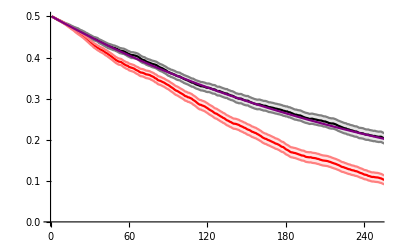

```mathematica
dynPlot[fileC,4,4]
```

## Heterozygosity Across Parameter Space

### LOESS Mean Smoothing

Project data onto the X=Y line.

```mathematica
Clear[dataNew]
dataNew[data_]:=dataNew[data]=Transpose[{Cos[Abs[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]]*Sqrt[Total[Transpose[data^2]]],Sin[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]*Sqrt[Total[Transpose[data^2]]]}]/.Indeterminate->0;
```

A gaussian weighting of the data  near the point xNew along the X=Y line

```mathematica
Clear[weights]
weights[xNew_,αW_,data_]:=weights[xNew,αW,data]=Exp[-(dataNew[data][[;;,1]]-xNew)^2/(2 αW^2)]//Chop;
```

Find the weighted mean and standard deviation and standard error.

```mathematica
Clear[meanNew]
meanNew[xNew_,αW_,data_]:=meanNew[xNew,αW,data]=Total[weights[xNew,αW,data]dataNew[data][[;;,2]]]/Total[weights[xNew,αW,data]]
```

```mathematica
SDNew[xNew_,αW_,data_]:=Sqrt[Total[weights[xNew,αW,data]*(dataNew[data][[;;,2]]-meanNew[xNew,αW,data])^2]/Total[weights[xNew,αW,data]]]
```

```mathematica
SENew[xNew_,αW_,data_]:=SDNew[xNew,αW,data]/Sqrt[Total[weights[xNew,αW,data]]]
```

The rolling average fit along the X+Y line (rotated plot)

```mathematica
Clear[RollFit]
RollFit[αW_,npts_,data_]:=RollFit[αW,npts,data]=Table[{x,meanNew[x,αW,data]},{x,0.001,Sqrt[2*0.5^2]-0.001,Sqrt[2*0.5^2]/npts}];
```

Projecting back into the original coordinates.

```mathematica
RollFitOld[αW_,npts_,data_]:=Transpose[{Cos[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2],Sin[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2]}]
```

### Variation within versus across replicates

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
VarVisual[rep_]:=Block[{temp},temp=Sort[Map[{#[[3]],1.96#[[4]]}&,HetCompMtrx2[fileC,rep,250]],#1[[1]]<#2[[1]]&];
ErrorListPlot[temp,PlotRange->{Min[Map[#[[1]]-#[[2]]&,temp]]0.95,Max[Map[#[[1]]+#[[2]]&,temp]]*1.05},Frame->True,FrameTicksStyle->Directive[Black,12],ImageSize->Medium,PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]]
```

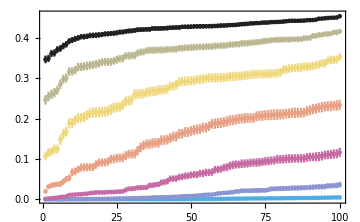

```mathematica
Show[Table[VarVisual[rep],{rep,1,7}],PlotRange->All]
Export[NotebookDirectory[]<>"Plots/Const_Variation.pdf",%,ImageResolution->300];
```

```mathematica
VarWB=Table[{Round[Mean[HetCompMtrx2[fileC,rep,250][[;;,4]]],0.0001],Round[StandardDeviation[HetCompMtrx2[fileC,rep,250][[;;,3]]],0.001],Round[StandardDeviation[HetCompMtrx2[fileC,rep,250][[;;,3]]]/Mean[HetCompMtrx2[fileC,rep,250][[;;,4]]],0.01]},{rep,1,7}]
```

{{0.0004,0.001,3.09},{0.0018,0.012,6.35},{0.004,0.037,9.25},{0.0058,0.061,10.5},{0.0058,0.059,10.2},{0.0044,0.037,8.46},{0.0029,0.022,7.65}}

```mathematica
Export[fileC2<>"VarWB.csv",VarWB]
```

/Users/ailenemacpherson/Desktop/EcoEpiDrift/sims_11_1/const_11_20/VarWB.csv

```mathematica
ErrorListPlot2[file_,rep_,τ_]:=Block[{temp},
temp=Sort[HetCompMtrx2[file,rep,τ],#1[[3]]<#2[[3]]&];
Show[ListLinePlot[Table[{{r,temp[[r,3]]-2temp[[r,4]]},{r,temp[[r,3]]+2temp[[r,4]]}},{r,1,100}],PlotStyle->Directive[Lighter[ColorData["CMYKColors"][(rep-1)/6]]],PlotRange->{0,0.5}],
ListPlot[Table[{r,temp[[r,3]]},{r,1,100}],PlotStyle->ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{"●",4}]
]
]
```

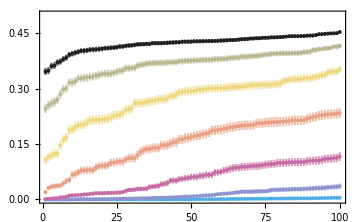

```mathematica
Show[Table[ErrorListPlot2[fileC,rep,250],{rep,1,7}],PlotRange->{0,0.5},Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
Export[NotebookDirectory[]<>"Plots/Const_Variation.pdf",%,ImageResolution->300];
```

### WF Diploid Over-dominance as a comparison

transition probability of i copies to j copies of the allele

```mathematica
w[i_,n_,s_]:=(i/n)(1-s)+(n-i)/n-((n-i)/n(1-s)+i/n)//Simplify
```

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(w[p[t]n,n,s])p[t](1-p[t])/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
p[i_,j_,n_,s_]:=If[i==0,If[j==0,1,0],If[i==n,If[j==n,1,0],Binomial[ n,j]((i/n (1+w[i,n,s]))/(i/n (1+w[i,n,s])+(n-i)/n (1+w[n-i,n,s])))^j(((n-i)/n (1+w[n-i,n,s]))/(i/n (1+w[i,n,s])+(n-i)/n (1+w[n-i,n,s])))^(n-j)]]
```

```mathematica
p0Vec[n_]:=Table[If[i==n/2,1,0],{i,0,n}]
```

```mathematica
Clear[tMtrx]
tMtrx[n_,s_]:=tMtrx[n,s]=Table[p[i,j,n,s],{j,0,n},{i,0,n}]
```

```mathematica
Clear[pOut]
pOut[n_,s_,t_]:=pOut[n,s,t]=MatrixPower[tMtrx[n,s],t].p0Vec[n]
```

```mathematica
hOver[n_,s_,t_]:=Table[2 i/n((n-i)/n),{i,0,n}].pOut[n,s,t]
```

```mathematica
hNeut[n_,t_]:=1/2 Exp[-t/n]
```

```mathematica
temp=Table[{hNeut[Round[10^npower,2],250],hOver[Round[10^npower,2],0.01,250]},{npower,2,2.75,0.25}]
```

$Aborted

```mathematica
temp={{1/(2 ⅇ^(5/2)),0.08992571775402472},{1/(2 ⅇ^(125/89)),0.23954849222376998},{1/(2 ⅇ^(125/158)),0.3742022797759149},{1/(2 ⅇ^(125/281)),0.443671355336855}};
```

```mathematica
HetOver=Join[{{0,0}},temp,{{0.5,0.5}}]//N;
```

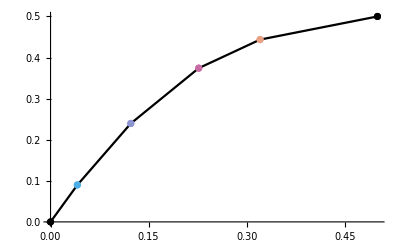

```mathematica
Show[ListLinePlot[HetOver,PlotStyle->Black],ListPlot[Map[{#}&,HetOver],PlotStyle->Join[{Black},Table[ ColorData["CMYKColors"][(rep-1)/6],{rep,1,4}],{Black}]]]
```

### Moran Diploid Over-dominance as a comparison

transition probability of i copies to j copies (out of n total copies) of the allele

```mathematica
w[i_,n_,s_]:=(i/n)(1-s)+(n-i)/n-((n-i)/n(1-s)+i/n)//Simplify
```

```mathematica
wA[i_,n_,s_]:=((i/n)(1-s)+(n-i)/n)/((i/n)^2(1-s)+2 i/n(n-i)/n+((n-i)/n)^2(1-s))
```

```mathematica
wa[i_,n_,s_]:=((n-i)/n(1-s)+i/n)/((i/n)^2(1-s)+2 i/n(n-i)/n+((n-i)/n)^2(1-s))
```

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(w[p[t]n,n,s])p[t](1-p[t])/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(wA[p[t]n,n,s]-1)p[t]/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
p[i_,j_,n_,s_]:=If[i==j,1-wA[i,n,s] i/n(n-i)/n-wa[i,n,s](n-i)/n i/n,If[j==i+1,wA[i,n,s] i/n(n-i)/n,If[j==i-1,wa[i,n,s](n-i)/n i/n,0]]]
```

```mathematica
p0Vec[n_]:=Table[If[i==n/2,1,0],{i,0,n}]
```

```mathematica
Clear[tMtrx]
tMtrx[n_,s_]:=tMtrx[n,s]=Table[p[i,j,n,s],{j,0,n},{i,0,n}]
```

```mathematica
Clear[pOut]
pOut[n_,s_,t_]:=pOut[n,s,t]=MatrixPower[tMtrx[n,s],t n].p0Vec[n]
```

```mathematica
hOver[n_,s_,t_]:=Table[2 i/n((n-i)/n),{i,0,n}].pOut[n,s,t]
```

```mathematica
hNeut[n_,t_]:=1/2 (1-2/n)^t//N
```

```mathematica
Clear[HetOver]
HetOver[s_,τ_]:=HetOver[s,τ]=Block[{temp},
temp=Table[{hNeut[Round[10^npower,2],250],hOver[Round[10^npower,2],s,τ]},{npower,2,3.25,0.25}];
Join[{{0,0}},temp,{{0.5,0.5}}]//N]
```

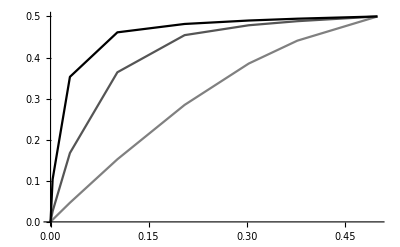

```mathematica
ListLinePlot[{HetOver[0.01,250],HetOver[0.05,250],HetOver[0.1,250]},PlotStyle->{Gray,Darker[Gray],Black}]
```

### Comparison to the simulated neutral expectation

```mathematica
Clear[meanData,sigData,nonSigData]
meanData[file_,τ_]:=meanData[file,τ]=Flatten[Table[HetCompMtrx2[file,rep,τ][[;;,{1,3}]],{rep,1,7}],1];
sigData[file_,rep_,τ_]:=sigData[file,rep,τ]=Select[HetCompMtrx2[file,rep,τ],(#[[3]]-2 #[[4]])>(#[[1]]+2#[[2]])||(#[[3]]+2 #[[4]])<(#[[1]]-2#[[2]])&];
nonSigData[file_,rep_,τ_]:=nonSigData[file,rep,τ]=Complement[HetCompMtrx2[file,rep,τ],sigData[file,rep,τ]];
PercentNeut[file_,rep_,τ_]:=Round[Length[nonSigData[file,rep,τ]]/(Length[sigData[file,rep,τ]]+Length[nonSigData[file,rep,τ]])*100]
```

```mathematica
meanPlot[file_,τ_]:=Show[
(*Plotting Data points*)
Table[
ListPlot[{sigData[file,rep,τ][[;;,{1,3}]],Complement[HetCompMtrx2[file,rep,τ],sigData[file,rep,τ]][[;;,{1,3}]]},PlotStyle-> ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{●,○}],{rep,1,7}],
(*Mean Fit and bootstrap fits*)
ListLinePlot[Table[RollFitOld[0.05,40,Bootstrap[meanData[file,τ],x]],{x,1,100}],PlotStyle->Directive[Pink (*Lighter[RGBColor[{163/255,56/255,75/255}]]*),Opacity[0.1]]],
ListLinePlot[RollFitOld[0.05,40,meanData[file,τ]],PlotStyle->Red (*RGBColor[{163/255,56/255,75/255}]*)],Plot[x,{x,0,0.5},PlotStyle->{Black,Thick,Dashing[0.02]}],
(*Compariosn to Overdominance*)
(*ListLinePlot[{HetOver[0.01,250],HetOver[0.05,250],HetOver[0.1,250]},PlotStyle->{Gray,Darker[Gray],Black}],*)
(*Plot Options*)
PlotRange->{{0,0.5},{0,0.5}},Frame->True,FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium(*,Epilog->Table[Text[Style[ToString[PercentNeut[file,rep,τ]],14,ColorData["CMYKColors"][rep/6]],{neutExp[10^(2+0.25 rep),τ],neutExp[10^(2+0.25 rep),τ]+0.07}/.{fH->1}(*Scaled[{0.1,0.1+(0.6-0.1)/7(6-rep)}]*)],{rep,0,6}]*)]
```

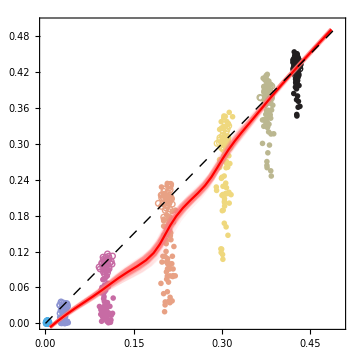

```mathematica
meanPlot[fileC2,250]//Quiet
Export[NotebookDirectory[]<>"Plots/Const_MeanHet_Rand.pdf",%,ImageResolution->300];
```

```mathematica
meanExport[file_,τ_]:=Transpose[Flatten[Join[{Transpose[RollFitOld[0.1,50,meanData[file,τ]]]},Table[Transpose[RollFitOld[0.1,50,Bootstrap[meanData[file,τ],x]]],{x,1,100}]],1]]
```

### Comparison to the Moran neutral expectation

```mathematica
meanPlot2[file_,τ_]:=Block[{tempMtrx,sigData,meanData},
tempMtrx[rep_]:=tempMtrx[rep]=Join[{Table[MoranNeut[file,run,rep][[τ]],{run,1,100}]},{Table[0,{run,1,100}]},Transpose[HetCompMtrx2[file,rep,τ][[;;,{3,4}]]]]//Transpose;
meanData=Flatten[Table[tempMtrx[rep][[;;,{1,3}]],{rep,1,7}],1];
sigData[rep_]:=sigData[rep]=Select[tempMtrx[rep],(#[[3]]-2 #[[4]])>(#[[1]]+2#[[2]])||(#[[3]]+2 #[[4]])<(#[[1]]-2#[[2]])&];
Show[
Table[
ListPlot[{sigData[rep][[;;,{1,3}]],Complement[tempMtrx[rep],sigData[rep]][[;;,{1,3}]]},PlotStyle-> ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{●,○}],{rep,1,7}],
ListLinePlot[Table[RollFitOld[0.05,40,Bootstrap[meanData,x]],{x,1,100}],PlotStyle->Directive[Pink,Opacity[0.1]]],
ListLinePlot[RollFitOld[0.05,40,meanData],PlotStyle->Red],Plot[x,{x,0,0.5},PlotStyle->{Black,Thick,Dashed}],PlotRange->{{0,0.5},{0,0.5}},Frame->True,AspectRatio->1]]
```

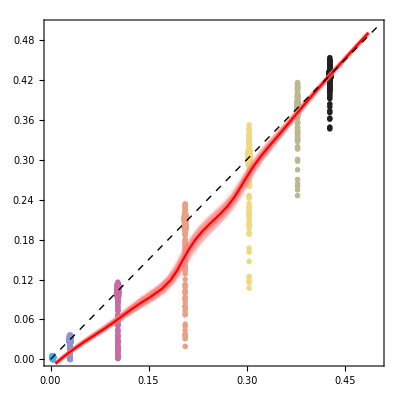

```mathematica
meanPlot2[fileC,250]
```

### Explaining Variation

#### Perturbations

```mathematica
γδPlot[file_,τ_]:=Block[{data,plot,min,max,lm},
data[rep_]:=Transpose[{Table[δ[file,run]-γ[file,run],{run,1,nRuns}],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min=Min[data[1][[;;,1]]];max=Max[data[1][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min,max},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Table[R2[rep]=lm[data[rep],"RSquared"],{rep,1,7}];
Table[Slope[rep]={lm[data[rep],"BestFitParameters"][[2]],lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]-lm[data[rep],"BestFitParameters"][[2]]},{rep,1,7}];
Show[Table[plot[rep],{rep,1,7}],PlotRange->{Automatic,{-0.2,0.1}},AxesOrigin->{0,0},Frame->True,FrameTicks->{{{-0.2,-0.1,0,0.1},False},{True,False}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
]
```

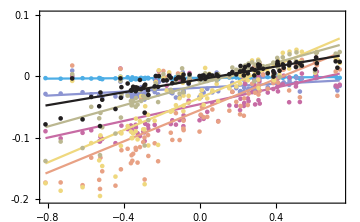

```mathematica
γδPlot[fileC,250]
Export[NotebookDirectory[]<>"Plots/Const_pert.pdf",%,ImageResolution->300];
```

```mathematica
Table[Join[Round[{R2[rep]},0.01],Round[Slope[rep],0.001]],{rep,1,7}]
Export[NotebookDirectory[]<>"RSquaredTemp.csv",%];
```

{{0.12,0.002,0.001},{0.24,0.016,0.006},{0.45,0.068,0.015},{0.58,0.127,0.022},{0.69,0.131,0.018},{0.7,0.086,0.011},{0.72,0.052,0.006}}

## Fixation Order

```mathematica
hostFixTime[file_,run_,rep_]:=Table[FirstPosition[state[file,run,rep][[{1,2},d,;;]],0.],{d,1,1000}]
```

```mathematica
pathFixTime[file_,run_,rep_]:=Table[FirstPosition[state[file,run,rep][[{3,4},d,;;]],0.],{d,1,1000}]
```

```mathematica
Clear[fixOrder]
fixOrder[file_,rep_]:=fixOrder[file,rep]=Block[{temp1,temp2,temp3,temp4,temp5,run,out},out={};
For[run=1,run≤100,run++,
(*All Data Points*)
temp1=Transpose[{hostFixTime[file,run,rep],pathFixTime[file,run,rep]}];
(*Host Fixed*)
temp2=DeleteCases[temp1,_?(#[[1]]==Missing["NotFound"]&)];
(*Host Fixed and Pathogen Fixed*)
temp3=DeleteCases[temp2,_?(#[[2]]==Missing["NotFound"]&)];
(*Pathogen Fixed then Host fixed*)
temp4=Select[temp3,#[[1,2]]>#[[2,2]]&];
AppendTo[out,{Length[temp1]-Length[temp2](*Host Polymorphic*),Length[temp2]-Length[temp3](*Host Fixed, Pathogen Polymorphic*),Length[temp3]-Length[temp4](*Host Fixed First*),Length[temp4](*Pathogen Fixed then Host Fixed*)}];
];
out/1000.
]
```

```mathematica
fixBarChart[file_,rep_,τ_]:=BarChart[fixOrder[file,rep][[Ordering[HetCompMtrx2[file,rep,τ][[;;,3]]]]],ChartLayout->"Stacked",ChartStyle->{Gray,Blue,Blue,Red},Frame->True,FrameTicks->{{{0,0.25,0.5,0.75,1},False},{True,False}},ImageSize->Medium,FrameTicksStyle->Directive[Black,16]]
```

Gray= Host and pathogen polymorphic at generation 250
Blue= Host fixed before pathogen
Red= Pathogen  fixes then host fixes
Green= Pathogen fixes, pathogen goes extinct, then host fixes
Runs (bars) are ordered in terms of increasing heterozygosity

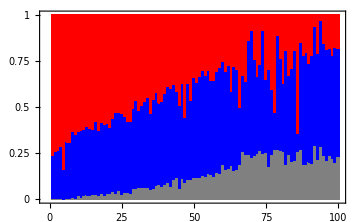

```mathematica
fixBarChart[fileC,4,250]
Export[NotebookDirectory[]<>"Plots/Const_DirSel_Rand.pdf",%,ImageResolution-> 300];
```

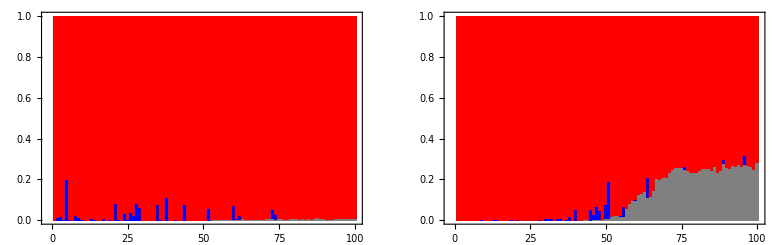

/Users/ailenemacpherson/Desktop/EcoEpiDrift/Plots/Const_DirSel_Comp.pdf

```mathematica
GraphicsRow[{fixBarChart[fileC,2,250],fixBarChart[fileC,4,250]}]
Export[NotebookDirectory[]<>"Plots/Const_DirSel_Comp.pdf",%,ImageResolution-> 300]
```